## Preparation

```mathematica
SetDirectory["/Users/marco/Lavoro/DiFF/Transversity/Global fit 2018/"]
```

/Users/marco/Lavoro/DiFF/h1 grid/Global fit 2018

```mathematica
Needs["ErrorBarLogPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["CustomTicks`"]
```

## Read data

Import data  for replica 600

```mathematica
dataLO=Import["grid/LO/xh1_PV18_LO_373.dat","Table"];
dataNLO=Import["grid/NLO/xh1_PV18_NLO_373.dat","Table"];
```

read x grid f

```mathematica
xgrid=dataLO//Take[#,{14,33}]&//Flatten;
```

read h1(x) for up and down, evolved at LO to Q=10 GeV

```mathematica
h1upLO=dataLO//Take[#,{2537,2636}]&//Transpose//#[[9]]&;
h1downLO=dataLO//Take[#,{2537,2636}]&//Transpose//#[[8]]&;
```

read h1(x) for up and down, evolved at NLO to Q=10 GeV

```mathematica
h1upNLO=dataNLO//Take[#,{2537,2636}]&//Transpose//#[[9]]&;
h1downNLO=dataNLO//Take[#,{2537,2636}]&//Transpose//#[[8]]&;
```

build ratio NLO/LO for up

```mathematica
ratio$up=h1upNLO/h1upLO;
```

## Plots

```mathematica
plotratio=Riffle[xgrid,ratio$up]//Partition[#,2]&;
```

```mathematica
xaxis=Table[{i,1},{i,0.0001,1,0.001}];
```

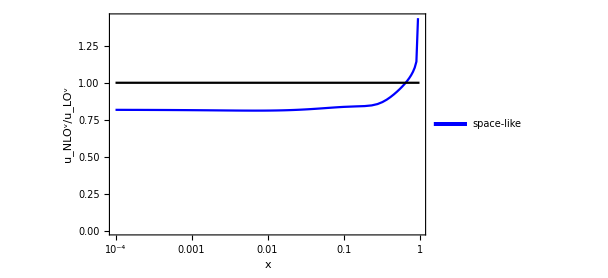

```mathematica
Show[ListLogLinearPlot[plotratio,Joined->True,PlotStyle->Blue,ImageSize->{450,300},BaseStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],LabelStyle->Directive[Black,FontFamily->"Helvetica-Bold",16],Frame->True,PlotLegends->Placed[LineLegend[{Directive[Blue,Thickness[0.008]]},{"space-like"}],{0.2,0.9}],FrameTicks->{{Automatic,None},{{{0.0001,"10^-4"},{0.0002,""},{0.0003,""},{0.0004,""},{0.0005,""},{0.0006,""},{0.0007,""},{0.0008,""},{0.0009,""},{0.001,"10^-3"},{0.002,""},{0.003,""},{0.004,""},{0.005,""},{0.006,""},{0.007,""},{0.008,""},{0.009,""},{0.01,"10^-2"},{0.02,""},{0.03,""},{0.04,""},{0.05,""},{0.06,""},{0.07,""},{0.08,""},{0.09,""},{0.1,"10^-1"},{0.2,""},{0.3,""},{0.4,""},{0.5,""},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1,"1"}},None}},PlotRange->{{0.0001,1},All},AxesOrigin->{0,0},FrameLabel->{{"u_NLO^v/u_LO^v",""},{"x","Q=10 GeV  replica 373"}}],ListLogLinearPlot[xaxis,Joined->True,PlotStyle->Black]]
(*Export["testNLO_LO_repl600.pdf",%]*)
```